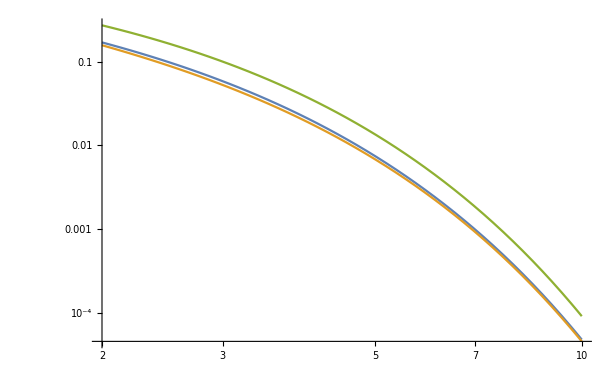

```mathematica
LogLogPlot[{ⅇ^-a(1/(2 a)+1),ⅇ^-a(1/(1-ⅇ^-a)),2 ⅇ^-a},{a,2,10},PlotRange->Full]
```

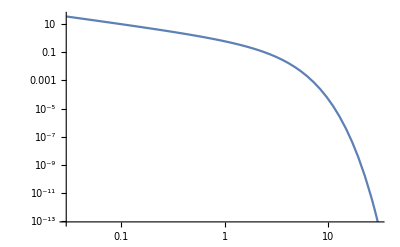

```mathematica
LogLogPlot[Abs[1/(1-ⅇ^-a)-1],{a,0,30}]
```

```mathematica
1/(1-ⅇ^((-2 π^2)/5))//N
```

1.01968

```mathematica
(1+ 1/π^2)//N
```

1.10132

```mathematica
Series[1/(1-ⅇ^-s),{s,0,9}]
```

1/s+1/2+s/12-s^3/720+s^5/30240-s^7/1209600+s^9/47900160+O[s]^10

```mathematica
Manipulate[Plot[{CDF[NormalDistribution[0,1/(√n)],x],
f[x,n],
f2[x,n]}
,{x,-3,3},
PlotRange->{{-3/(√n),3/(√n)},{0,1}}],
{n,1,50}]
```

```mathematica
f[t_,n_]:= 1/(√n)∑_(k=-3*√n)^Floor[t √n] PDF[NormalDistribution[0,1/(√n)],k/(√n)]
```

```mathematica
f2[t_,n_]:=1/n ∑_(k=-3*n)^(t n) PDF[NormalDistribution[0,1/(√n)],k/n]
```

```mathematica
Table[∑_(k=-3*n)^(3*n) PDF[NormalDistribution[0,1/(√n)],k/n]/n,{n,1,30}]//N
```

{0.999729,0.999997,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

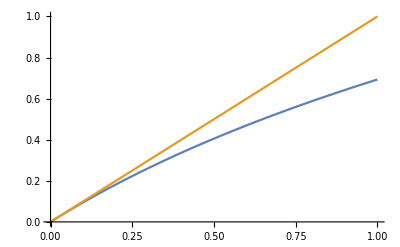

```mathematica
Plot[{Log[1+x],x},{x,0,1}]
```

```mathematica
Series[ⅇ^x,{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
2(1+4 π^2)∑_(j=1)^∞ j^2 Exp[-2 π^2 j^2]//N
```

2.16583×10^-7

```mathematica
(√(2π))/x∑_(k=1)^30 ⅇ^(-(2k-1)^2 π^2/(8 x^2))/. x-> 0.01
```

3.20388915761093×10^-5356

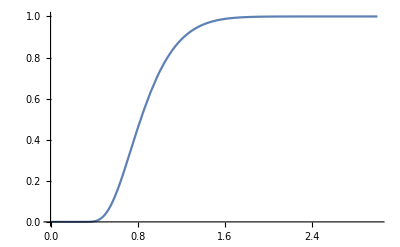

```mathematica
Plot[(√(2π))/x∑_(k=1)^30 ⅇ^(-(2k-1)^2 π^2/(8 x^2)),{x,0,3},PlotRange->Full]
```

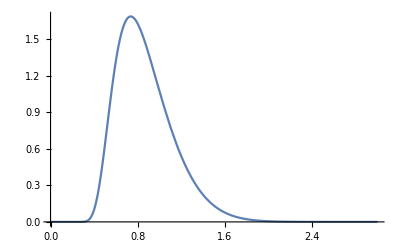

```mathematica
Plot[Evaluate[D[(√(2π))/x∑_(k=1)^30 ⅇ^(-(2k-1)^2 π^2/(8 x^2)),x]],{x,0,3},PlotRange->Full]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

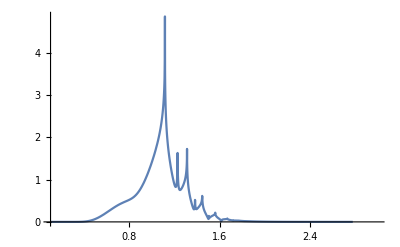

```mathematica
Plot[Abs[-(ⅇ^((3 π^2)/(8 x^2)) (ⅇ^(-π^2/(2 x^2)))^(3/4) √(π/2) EllipticTheta[2,0,ⅇ^(-π^2/(2 x^2))])/x^2+(ⅇ^(-π^2/(8 x^2)) (ⅇ^(-π^2/(2 x^2)))^(3/4) π^(5/2) Derivative[0,0,1][EllipticTheta][2,0,ⅇ^(-π^2/(2 x^2))])/(√2 x^4)],{x,0.1,3},PlotRange->Full]
```

```mathematica
ⅇ^-ⅈ/ⅈ^(1/2)//N
```

-0.212958-0.977061 ⅈ

```mathematica
ⅇ^-ⅈ/ⅈ^(1/2)
```

```mathematica
∫_0^∞ ⅇ^-t/(√t)ⅆt
```

√π

```mathematica
∫_-ⅈ^∞ ⅇ^-t/t ⅆt
```

ⅈ π-ExpIntegralEi[ⅈ]

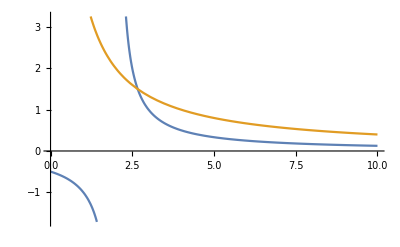

```mathematica
Plot[{1/(z-2),4/z},{z,0,10}]
```

```mathematica
√7.1
```

2.66458

```mathematica
3 Log[2]//N
```

2.07944

```mathematica
Solve[((√2)/2)/(x-3Log[2])==1/x,x]
```

{{x→(6 Log[2])/(2-√2)}}

```mathematica
(6 Log[2])/(2-√2)//N
```

7.09966

```mathematica
√((6 Log[2])/(2-√2))//N
```

2.66452

```mathematica
2
```

```mathematica
FourierTransform[(1-ⅇ^(-2 n(g2-y)(g1-x)))If[y < g1,1,0],x,s,FourierParameters->{0,-2Pi}] //Simplify
```

DiracDelta[s] If[y<g1,1,0]-2 ⅇ^(-2 g1 n (g2-y)) π DiracDelta[2 ⅈ g2 n+2 π s-2 ⅈ n y] If[y<g1,1,0]

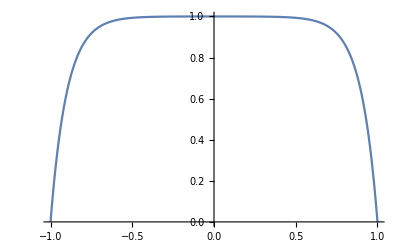

```mathematica
Plot[1-ⅇ^(-2*5*(1-x))-ⅇ^(-2*5*(-1-x)(-1-0)),{x,-1,1},PlotRange->Full]
```

```mathematica
FourierTransform[(1-ⅇ^(-2 n(g1u-x)(g2u-y))-ⅇ^(-2 n(g1l-x)(g2l-y)))If[y > g2l && y < g2u,1,0],y,s,FourierParameters->{0,-2Pi}] //Simplify
```

Piecewise[{{(ⅇ^(-2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (π s (ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (g1l-g1u) n+ⅇ^(2 n (g1l g2u+g1u g2u+2 g2l x)) (g1u n-ⅈ π s-n x)+ⅇ^(2 n (g1l g2l+g1u g2l+2 g2u x)) (-g1l n+ⅈ π s+n x)) Cos[(g2l-g2u) π s]+(ⅇ^(2 n (g1l g2l+g1u g2l+2 g2u x)) π s (ⅈ g1l n+π s-ⅈ n x)+ⅇ^(2 n (g1l g2u+g1u g2u+2 g2l x)) π s (ⅈ g1u n+π s-ⅈ n x)+ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) n (-ⅈ g1u π s-2 g1u n x+2 ⅈ π s x+2 n x^2+g1l (2 g1u n-ⅈ π s-2 n x))) Sin[(g2l-g2u) π s]) (Cos[(g2l+g2u) π s]-ⅈ Sin[(g2l+g2u) π s]))/(2 π s (ⅈ g1l n+π s-ⅈ n x) (ⅈ g1u n+π s-ⅈ n x)), g2l<g2u}, {0, True}}]

```mathematica
(ⅇ^(-2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (π s (ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (g1l-g1u) n+ⅇ^(2 n (g1l g2u+g1u g2u+2 g2l x)) (g1u n-ⅈ π s-n x)+ⅇ^(2 n (g1l g2l+g1u g2l+2 g2u x)) (-g1l n+ⅈ π s+n x)) Cos[(g2l-g2u) π s]+(ⅇ^(2 n (g1l g2l+g1u g2l+2 g2u x)) π s (ⅈ g1l n+π s-ⅈ n x)+ⅇ^(2 n (g1l g2u+g1u g2u+2 g2l x)) π s (ⅈ g1u n+π s-ⅈ n x)+ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) n (-ⅈ g1u π s-2 g1u n x+2 ⅈ π s x+2 n x^2+g1l (2 g1u n-ⅈ π s-2 n x))) Sin[(g2l-g2u) π s]) (Cos[(g2l+g2u) π s]-ⅈ Sin[(g2l+g2u) π s]))/(2 π s (ⅈ g1l n+π s-ⅈ n x) (ⅈ g1u n+π s-ⅈ n x))//FullSimplify
```

(ⅇ^(-ⅈ (g2l+g2u) π s-2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (π s (ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (g1l-g1u) n+ⅇ^(2 (g1l+g1u) g2u n+4 g2l n x) (g1u n-ⅈ π s-n x)+ⅇ^(2 (g1l+g1u) g2l n+4 g2u n x) (-g1l n+ⅈ π s+n x)) Cos[(g2l-g2u) π s]+(ⅇ^(2 (g1l+g1u) g2l n+4 g2u n x) π s (π s+ⅈ n (g1l-x))+ⅇ^(2 (g1l+g1u) g2u n+4 g2l n x) π s (π s+ⅈ n (g1u-x))+ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) n (2 g1l g1u n-ⅈ g1l π s-ⅈ g1u π s-2 ((g1l+g1u) n-ⅈ π s) x+2 n x^2)) Sin[(g2l-g2u) π s]))/(2 π s (g1l n-ⅈ π s-n x) (-g1u n+ⅈ π s+n x))

```mathematica
fhat[s_]:=(ⅇ^(-ⅈ (g2l+g2u) π s-2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (π s (ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) (g1l-g1u) n+ⅇ^(2 (g1l+g1u) g2u n+4 g2l n x) (g1u n-ⅈ π s-n x)+ⅇ^(2 (g1l+g1u) g2l n+4 g2u n x) (-g1l n+ⅈ π s+n x)) Cos[(g2l-g2u) π s]+(ⅇ^(2 (g1l+g1u) g2l n+4 g2u n x) π s (π s+ⅈ n (g1l-x))+ⅇ^(2 (g1l+g1u) g2u n+4 g2l n x) π s (π s+ⅈ n (g1u-x))+ⅇ^(2 n (g1l g2l+g1u g2u+(g2l+g2u) x)) n (2 g1l g1u n-ⅈ g1l π s-ⅈ g1u π s-2 ((g1l+g1u) n-ⅈ π s) x+2 n x^2)) Sin[(g2l-g2u) π s]))/(2 π s (g1l n-ⅈ π s-n x) (-g1u n+ⅈ π s+n x))
```

```mathematica
ghat[s_]:=ⅇ^(-(2 π s (π s+ⅈ n x))/n)
```

```mathematica
∫_(-∞)^∞ fhat[s-t]ghat[t]ⅆt
```

$Aborted

```mathematica
FourierTransform[(1-ⅇ^(-2 n(g0-x0)z))(1-ⅇ^(-2 n(g2-x2)z))If[z > 0,1,0],z,s,FourierParameters->{0,-2Pi}] //Simplify
```

(ⅈ n^2 (g0-x0) (g2-x2) (g0 n+g2 n+2 ⅈ π s-n x0-n x2))/(2 π s (-ⅈ g0 n+π s+ⅈ n x0) (g0 n+g2 n+ⅈ π s-n x0-n x2) (-ⅈ g2 n+π s+ⅈ n x2))

```mathematica
Series[(ⅈ n^2 (g0-x0) (g2-x2) (g0 n+g2 n+2 ⅈ π s-n x0-n x2))/(2 π s (-ⅈ g0 n+π s+ⅈ n x0) (g0 n+g2 n+ⅈ π s-n x0-n x2) (-ⅈ g2 n+π s+ⅈ n x2)),{s,∞,4}]
```

(ⅈ n^2 (g0-x0) (g2-x2))/(π^3 s^3)-(3 (n^3 (g0-x0) (g2-x2) (g0+g2-x0-x2)))/(2 π^4 s^4)+O[1/s]^5

```mathematica
FourierTransform[(1-ⅇ^(-2 n(g1-x)z))If[z > 0,1,0],z,s,FourierParameters->{0,-2Pi}] //Simplify
```

(g1 n-n x)/(2 ⅈ g1 n π s-2 π^2 s^2-2 ⅈ n π s x)

```mathematica
Series[(g1 n-n x)/(2 ⅈ g1 n π s-2 π^2 s^2-2 ⅈ n π s x),{s,∞,4}]
```

-(g1 n-n x)/(2 π^2 s^2)-(ⅈ (g1 n-n x)^2)/(2 π^3 s^3)+(g1 n-n x)^3/(2 π^4 s^4)+O[1/s]^5

```mathematica
FourierTransform[PDF[NormalDistribution[0,1/(√n)],y-x],y,s,FourierParameters->{0,-2Pi}] //Simplify
```

ⅇ^(-(2 π s (π s+ⅈ n x))/n)

```mathematica
∫_(-∞)^∞ ⅇ^(-(2 (π s)^2)/n)ⅇ^(-2 π s ⅈ (g1-x))(g1 n-n x)/(2 ⅈ n π s(g1-x)-2 π^2 s^2)ⅆs
```

$Aborted

```mathematica
(g1 n-n x)∫_(-∞)^∞ ⅇ^(-(2 (π (s-t))^2)/n)ⅇ^(-2 π (t-s) ⅈ (g1-x))1/(2 ⅈ n π t(g1-x)-2 π^2 t^2)ⅆt
```

Integrate::idiv: Integral of (ⅇ^(-(2 π^2 (s-t)^2)/n-2 ⅈ π (-s+t) (g1-x)))/(-2 π^2 t^2+2 ⅈ n π t (g1-x)) does not converge on {-∞,∞}.

(g1 n-n x) ∫_(-∞)^∞ (ⅇ^(-(2 π^2 (s-t)^2)/n-2 ⅈ π (-s+t) (g1-x)))/(-2 π^2 t^2+2 ⅈ n π t (g1-x))ⅆt

```mathematica
(g1 n-n x)∫_(-∞)^∞ ⅇ^(-(2 (π (s-t))^2)/n)ⅇ^(-2 π (s-t) ⅈ (g1-x))1/(2 ⅈ n π t(g1-x)-2 π^2 t^2)ⅆt
```

(g1 n-n x) ∫_(-∞)^∞ (ⅇ^(-(2 π^2 (s-t)^2)/n-2 ⅈ π (s-t) (g1-x)))/(-2 π^2 t^2+2 ⅈ n π t (g1-x))ⅆt

```mathematica
(g1 n-n x)∫_(-∞)^∞ ⅇ^(-(2 (π t)^2)/n)ⅇ^(-2 π (t) ⅈ (g1-x))1/(2 ⅈ n π (s-t)(g1-x)-2 π^2 (s-t)^2)ⅆt
```

$Aborted

```mathematica
Abs[ⅇ^(-(2 (π (t-s))^2)/n)ⅇ^(-2 π (t-s) ⅈ (g1-x))]
```

ⅇ^(2 π Im[(-s+t) (g1-x)]-2 π^2 Re[(-s+t)^2/n])

```mathematica
∫_(-∞)^∞ ⅇ^(-(2 (π t)^2)/n)(n(g1 - x))/(2 π^2 (s-t)^2)ⅆt
```

ConditionalExpression[-(ⅇ^(-(2 π^2 s^2)/n) (g1-x) (√2 ⅇ^((2 π^2 s^2)/n) √n-2 π^(3/2) s Erfi[(√2 π s)/(√n)]+2 √π s Log[-1/s]+2 √π s Log[s]))/(√π),Re[n]>0&&Im[s]≠0]

```mathematica
-(ⅇ^(-(2 π^2 s^2)/n) (g1-x) (√2 ⅇ^((2 π^2 s^2)/n) √n-2 π^(3/2) s Erfi[(√2 π s)/(√n)]+2 √π s Log[-1/s]+2 √π s Log[s]))/(√π)//FullSimplify
```

(g1-x) (-√n √(2/π)+2 ⅇ^(-(2 π^2 s^2)/n) s (π Erfi[(√2 π s)/(√n)]-Log[-1/s]-Log[s]))

```mathematica
(n(g1 - x))/(2 π^2)∫_(-∞)^∞ ⅇ^(-(2 (π t)^2)/n)1/(s-t)^2 ⅆt
```

ConditionalExpression[(n (g1-x) (-(2 √2 π^(3/2))/(√n)+(4 ⅇ^(-(2 π^2 s^2)/n) π^2 s (π Erfi[(√2 π s)/(√n)]-Log[-1/s]-Log[s]))/n))/(2 π^2),Re[n]>0&&Im[s]≠0]

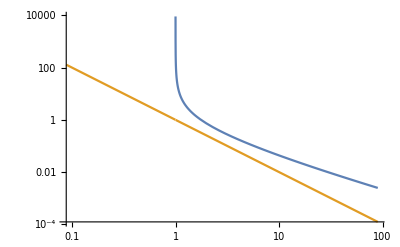

```mathematica
LogLogPlot[{1/(s Log[s]),1/s^2},{s,0,90}]
```

```mathematica
∫_(-∞)^∞ ⅇ^(-(2 (π( s-t))^2)/n)1/t^2 ⅆt
```

Integrate::idiv: Integral of (ⅇ^(-(2 π^2 (s-t)^2)/n))/t^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ (ⅇ^(-(2 π^2 (s-t)^2)/n))/t^2 ⅆt

```mathematica
∫_(-∞)^∞ ⅇ^(-(2 (π t)^2)/n)1/(s-t)^2 ⅆt
```

ConditionalExpression[-(2 √2 π^(3/2))/(√n)+(4 ⅇ^(-(2 π^2 s^2)/n) π^2 s (π Erfi[(√2 π s)/(√n)]-Log[-1/s]-Log[s]))/n,Re[n]>0&&Im[s]≠0]

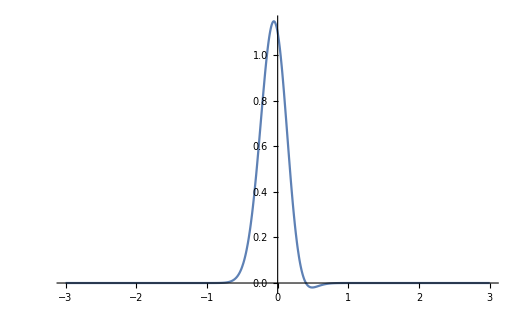

```mathematica
Plot[(1-ⅇ^(-2(0.4-x)))PDF[NormalDistribution[0,1/5],x ],{x,-3,3},PlotRange->Full]
```

```mathematica
FourierTransform[(1 - ⅇ^(-2n(g2-y)(g1 - x)))PDF[NormalDistribution[0,1/(√n)],y-x],y,s,FourierParameters->{0,-2Pi}] //Simplify
```

ⅇ^(-(2 π s (π s+ⅈ n x))/n)-ⅇ^(-2 g2 n (g1-x)-(n x^2)/2+(-2 g1 n+2 ⅈ π s+n x)^2/(2 n))

```mathematica
ⅇ^(-(2 π s (π s+ⅈ n x))/n)-ⅇ^(-2 g2 n (g1-x)-(n x^2)/2+(-2 g1 n+2 ⅈ π s+n x)^2/(2 n))//FullSimplify
```

-ⅇ^(-(2 π s (π s+ⅈ n x))/n) (-1+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)))

```mathematica
ComplexExpand[Abs[ⅇ^(-(2 π s (π s+ⅈ n x))/n)-ⅇ^(-2 g2 n (g1-x)-(n x^2)/2+(-2 g1 n+2 ⅈ π s+n x)^2/(2 n))]]//Simplify
```

√(ⅇ^(-4 g1 g2 n-(4 π^2 s^2)/n+n (4 g2-x) x) (ⅇ^(n (-2 g1+x)^2)+ⅇ^(n (4 g1 g2-4 g2 x+x^2))-2 ⅇ^(n (2 g1^2+2 g1 (g2-x)+x (-2 g2+x))) Cos[4 π s (g1-x)]))

```mathematica
ComplexExpand[Abs[ⅇ^(-(2 π s (π s+ⅈ n x))/n)]]//Simplify
```

ⅇ^(-(2 π^2 s^2)/n)

```mathematica
ComplexExpand[Abs[ⅇ^(-2 g2 n (g1-x)-(n x^2)/2+(-2 g1 n+2 ⅈ π s+n x)^2/(2 n))]]//Simplify
```

ⅇ^(2 g1^2 n-(2 π^2 s^2)/n+2 g2 n x-2 g1 n (g2+x))

```mathematica
fhat2[s_]:=ⅇ^(-(2 π^2 s^2)/n)+ⅇ^(2 g1^2 n-(2 π^2 s^2)/n+2 g2 n x-2 g1 n (g2+x))
```

```mathematica
ghat2[s_]:=1/(2π s)
```

```mathematica
∫_(-∞)^∞ fhat2[s-t]ghat2[t]ⅆt
```

Integrate::idiv: Integral of (ⅇ^(-(2 π^2 (s-t)^2)/n))/(2 π t)+(ⅇ^(-(2 π^2 («1»)^2)/n-2 g1 n (g2+x)+2 n (g1^2+g2 x)))/(2 π t) does not converge on {-∞,∞}.

∫_(-∞)^∞ (ⅇ^(-(2 π^2 (s-t)^2)/n)+ⅇ^(2 g1^2 n-(2 π^2 (s-t)^2)/n+2 g2 n x-2 g1 n (g2+x)))/(2 π t)ⅆt

```mathematica
∫_(-∞)^∞ fhat2[t]ghat2[s-t]ⅆt
```

ConditionalExpression[(ⅇ^(-(2 π^2 s^2)/n-2 g1 n (g2+x)) (ⅇ^(2 g1 n (g2+x))+ⅇ^(2 n (g1^2+g2 x))) (π Erfi[(√2 π s)/(√n)]-Log[-1/s]-Log[s]))/(2 π),Re[n]>0&&Im[s]≠0]

```mathematica
(ⅇ^(-(2 π^2 s^2)/n-2 g1 n (g2+x)) (ⅇ^(2 g1 n (g2+x))+ⅇ^(2 n (g1^2+g2 x))) (π Erfi[(√2 π s)/(√n)]-Log[-1/s]-Log[s]))/(2 π)//Simplify
```

(ⅇ^(-(2 π^2 s^2)/n-2 g1 n (g2+x)) (ⅇ^(2 g1 n (g2+x))+ⅇ^(2 n (g1^2+g2 x))) (π Erfi[(√2 π s)/(√n)]-Log[-1/s]-Log[s]))/(2 π)

```mathematica
Exp[ⅇ^(-2 g1 n (g2+x)+2 n (g1^2+g2 x))]//Simplify
```

ⅇ^(ⅇ^(2 (g1-g2) n (g1-x)))

```mathematica
Plot[Abs[]]
```

```mathematica
FourierTransform[If[y < g2,1,0],y,s,FourierParameters->{0,-2Pi}] //Simplify
```

(ⅈ Cos[2 g2 π s]+Sin[2 g2 π s])/(2 π s)

```mathematica
Abs[(ⅈ Cos[2 g2 π s]+Sin[2 g2 π s])/(2 π s)]
```

Abs[(ⅈ Cos[2 g2 π s]+Sin[2 g2 π s])/s]/(2 π)

```mathematica
(ⅈ Cos[2 g2 π s]+Sin[2 g2 π s])/(2 π s)//ExpToTrig
```

(ⅈ Cos[2 g2 π s])/(2 π s)+Sin[2 g2 π s]/(2 π s)

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-3,3}]
```

```mathematica
D[(1 - ⅇ^(-2n(g2-y)(g1 - x)))PDF[NormalDistribution[0,1/(√n)],y-x],{y,2}]
```

1/(√(2 π))√n (-4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x)^2+4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x) (-x+y)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2))

```mathematica
FourierTransform[(1 - ⅇ^(-2n(g2-y)(g1 - x)))PDF[NormalDistribution[0,1/(√n)],y-x],y,s,FourierParameters->{0,-2Pi}] //Simplify
```

```mathematica
1/(√(2 π))√n (-4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x)^2+4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x) (-x+y)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2))
```